# Tetraedro con α, β, δ y ξ: -Graphics-

|z_1 ⟩ = (α
β)		|ω_1 ⟩ = (α
β)
|z_2 ⟩ = (α
-β)		|ω_2 ⟩ = (α
-β)
|z_3 ⟩ = (ξ
δ ⅇ^(ⅈ θ))	|ω_3 ⟩ = (ξ
δ ⅇ^(ⅈ φ))
|z_4 ⟩ = (ξ
-δ ⅇ^(ⅈ θ))	|ω_4 ⟩ = (ξ
-δ ⅇ^(ⅈ φ))

θ = cte. , φ = cte.

## Modules:

## LaTeX for Mathematica

```mathematica
ResourceFunction["MaTeXInstall"][];
<<MaTeX`
```

## Main module

```mathematica
main[parameters_]:=Module[{array=parameters},

{xmin, xmax}={array[["xmin"]], array[["xmax"]]};
{γ,λ}={array[["γ"]], array[["λ"]]};
{α0,β0,ξ0,δ0}={array[["α0"]],array[["β0"]],array[["ξ0"]],array[["δ0"]]};
{θ,φ}={array[["θ"]], array[["φ"]]};
manirange=array[["3drange"]];
ndsolvemethod=array[["method"]];
name=array[["name"]];
magni=1.5;
t00 = array[["tiempo"]];

file="/Users/enekoaranguren/Documents/master/tfm/codigos/plots/tetra/";
gifname=file<>name<>"/";

(* *)
Eα[t_]={{Abs[α[t]]^2+Abs[β[t]]^2,Abs[α[t]]^2-Abs[β[t]]^2,α[t]* ξ[t]+β[t]* δ[t] ⅇ^(ⅈ θ), α[t]* ξ[t]-β[t]* δ[t] ⅇ^(ⅈ θ)},
	       {Abs[α[t]]^2-Abs[β[t]]^2, Abs[α[t]]^2+Abs[β[t]]^2,α[t]* ξ[t]-β[t]* δ[t] ⅇ^(ⅈ θ),α[t]* ξ[t]+β[t]* δ[t] ⅇ^(ⅈ θ)},
	       {α[t] ξ[t]*+β[t] δ[t]* ⅇ^(-ⅈ θ),α[t] ξ[t]*-β[t] δ[t]* ⅇ^(-ⅈ θ),Abs[ξ[t]]^2+Abs[δ[t]]^2,Abs[ξ[t]]^2-Abs[δ[t]]^2},
	       {α[t] ξ[t]*-β[t] δ[t]* ⅇ^(-ⅈ θ),α[t] ξ[t]*+β[t] δ[t]* ⅇ^(-ⅈ θ),Abs[ξ[t]]^2-Abs[δ[t]]^2,Abs[ξ[t]]^2+Abs[δ[t]]^2}};

Fcα[t_]={{0, -2α[t]*β[t]*, -β[t]*ξ[t]*+α[t]*δ[t]*ⅇ^(-ⅈ θ),-β[t]*ξ[t]*-α[t]*δ[t]*ⅇ^(-ⅈ θ)},
		{2α[t]*β[t]*, 0, β[t]*ξ[t]*+α[t]*δ[t]*ⅇ^(-ⅈ θ),β[t]*ξ[t]*-α[t]*δ[t]*ⅇ^(-ⅈ θ)},
		{β[t]*ξ[t]*-α[t]*δ[t]*ⅇ^(-ⅈ θ),  -β[t]*ξ[t]*-α[t]*δ[t]*ⅇ^(-ⅈ θ), 0,-2ξ[t]*δ[t]*ⅇ^(-ⅈ θ)},
		{β[t]*ξ[t]*+α[t]*δ[t]*ⅇ^(-ⅈ θ),-β[t]*ξ[t]*+α[t]*δ[t]*ⅇ^(-ⅈ θ), 2ξ[t]*δ[t]*ⅇ^(-ⅈ θ),0}};

Eβ[t_]={{Abs[α[t]]^2+Abs[β[t]]^2,Abs[α[t]]^2-Abs[β[t]]^2, α[t]* ξ[t]+β[t]* δ[t] ⅇ^(ⅈ φ),α[t]* ξ[t]-β[t]* δ[t] ⅇ^(ⅈ φ)},
	       {Abs[α[t]]^2-Abs[β[t]]^2, Abs[α[t]]^2+Abs[β[t]]^2,α[t]* ξ[t]-β[t]* δ[t] ⅇ^(ⅈ φ),α[t]* ξ[t]+β[t]* δ[t] ⅇ^(ⅈ φ)},
	       {α[t] ξ[t]*+β[t] δ[t]* ⅇ^(-ⅈ φ),α[t] ξ[t]*-β[t] δ[t]* ⅇ^(-ⅈ φ),Abs[ξ[t]]^2+Abs[δ[t]]^2,Abs[ξ[t]]^2-Abs[δ[t]]^2},
	       {α[t] ξ[t]*-β[t] δ[t]* ⅇ^(-ⅈ φ),α[t] ξ[t]*+β[t] δ[t]* ⅇ^(-ⅈ φ),Abs[ξ[t]]^2-Abs[δ[t]]^2,Abs[ξ[t]]^2+Abs[δ[t]]^2}};

Fcβ[t_]={{0, -2α[t]*β[t]*, -β[t]*ξ[t]*+α[t]*δ[t]*ⅇ^(-ⅈ φ),-β[t]*ξ[t]*-α[t]*δ[t]*ⅇ^(-ⅈ φ)},
		{2α[t]*β[t]*, 0, β[t]*ξ[t]*+α[t]*δ[t]*ⅇ^(-ⅈ φ),β[t]*ξ[t]*-α[t]*δ[t]*ⅇ^(-ⅈ φ)},
		{β[t]*ξ[t]*-α[t]*δ[t]*ⅇ^(-ⅈ φ),  -β[t]*ξ[t]*-α[t]*δ[t]*ⅇ^(-ⅈ φ), 0,-2ξ[t]*δ[t]*ⅇ^(-ⅈ φ)},
		{β[t]*ξ[t]*+α[t]*δ[t]*ⅇ^(-ⅈ φ),-β[t]*ξ[t]*+α[t]*δ[t]*ⅇ^(-ⅈ φ), 2ξ[t]*δ[t]*ⅇ^(-ⅈ φ),0}};
(* *)

(*
spinor[t] = {spi1[t],spi2[t],spi3[t],spi4[t]};
spi1[t]={α[t],β[t]};
spi2[t]={α[t],-β[t]};
spi3[t]={ξ[t],δ[t]ⅇ^(ⅈ θ)};
spi4[t]={ξ[t],-δ[t]ⅇ^(ⅈ θ)};
*)

eq1= α'[t]== ∑_(l=1)^4 (-ⅈ λ[[1,l]] Eβ[t][[1,l]] spinor[t][[l]][[1]]+2ⅈ γ[[1,l]]*Fcβ[t][[1,l]](-spinor[t][[l]][[2]]*));
eq2 = β'[t]==∑_(l=1)^4 (-ⅈ λ[[1,l]] Eβ[t][[1,l]] spinor[t][[l]][[2]]+2ⅈ γ[[1,l]]*Fcβ[t][[1,l]](spinor[t][[l]][[1]]*));
eq3= ξ'[t]==∑_(l=1)^4 (-ⅈ λ[[3,l]] Eβ[t][[3,l]] spinor[t][[l]][[1]]+2ⅈ γ[[3,l]]*Fcβ[t][[3,l]](-spinor[t][[l]][[2]]*));
eq4= δ'[t]==∑_(l=1)^4 (-ⅈ λ[[3,l]] Eβ[t][[3,l]] spinor[t][[l]][[2]]+2ⅈ γ[[3,l]]*Fcβ[t][[3,l]](spinor[t][[l]][[1]]*))ⅇ^(-ⅈ θ);

soluα=NDSolve[{eq1,eq2,eq3, eq4, α[0]==α0, β[0]==β0, ξ[0]==ξ0, δ[0]==δ0}, α,{t,  xmin, xmax},Method-> ndsolvemethod/._Missing-> "Automatic"];
soluβ=NDSolve[{eq1,eq2, eq3, eq4, α[0]==α0, β[0]==β0, ξ[0]==ξ0, δ[0]==δ0}, β, {t, xmin, xmax},Method-> ndsolvemethod/._Missing-> "Automatic"];
soluξ=NDSolve[{eq1,eq2, eq3, eq4, α[0]==α0, β[0]==β0, ξ[0]==ξ0, δ[0]==δ0}, ξ, {t, xmin, xmax},Method-> ndsolvemethod/._Missing-> "Automatic"];
soluδ=NDSolve[{eq1,eq2, eq3, eq4, α[0]==α0, β[0]==β0, ξ[0]==ξ0, δ[0]==δ0}, δ, {t, xmin, xmax},Method-> ndsolvemethod/._Missing-> "Automatic"];

solutions=Flatten[{soluα,soluβ,soluξ,soluδ}];
(*
regular=Check[{soluα=NDSolve[{eq1,eq2,eq3, eq4, α[0]==α0, β[0]==β0, ξ[0]==ξ0, δ[0]==δ0}, α,{t,  xmin, xmax},Method-> ndsolvemethod/._Missing-> "Automatic"];
soluβ=NDSolve[{eq1,eq2, eq3, eq4, α[0]==α0, β[0]==β0, ξ[0]==ξ0, δ[0]==δ0}, β, {t, xmin, xmax},Method-> ndsolvemethod/._Missing-> "Automatic"];
soluξ=NDSolve[{eq1,eq2, eq3, eq4, α[0]==α0, β[0]==β0, ξ[0]==ξ0, δ[0]==δ0}, ξ, {t, xmin, xmax},Method-> ndsolvemethod/._Missing-> "Automatic"];
soluδ=NDSolve[{eq1,eq2, eq3, eq4, α[0]==α0, β[0]==β0, ξ[0]==ξ0, δ[0]==δ0}, δ, {t, xmin, xmax},Method-> ndsolvemethod/._Missing-> "Automatic"]},Null];
Print["REGULAR"];

If[regular==Null,
regular="Div",
regular="No-Div"];

Print[regular];

Hamiltonian;
Eα[t_]={{Abs[α[t]]^2+Abs[β[t]]^2,Abs[α[t]]^2-Abs[β[t]]^2,α[t]* ξ[t]+β[t]* δ[t] ⅇ^(ⅈ θ), α[t]* ξ[t]-β[t]* δ[t] ⅇ^(ⅈ θ)},
	       {Abs[α[t]]^2-Abs[β[t]]^2, Abs[α[t]]^2+Abs[β[t]]^2,α[t]* ξ[t]-β[t]* δ[t] ⅇ^(ⅈ θ),α[t]* ξ[t]+β[t]* δ[t] ⅇ^(ⅈ θ)},
	       {α[t] ξ[t]*+β[t] δ[t]* ⅇ^(-ⅈ θ),α[t] ξ[t]*-β[t] δ[t]* ⅇ^(-ⅈ θ),Abs[ξ[t]]^2+Abs[δ[t]]^2,Abs[ξ[t]]^2-Abs[δ[t]]^2},
	       {α[t] ξ[t]*-β[t] δ[t]* ⅇ^(-ⅈ θ),α[t] ξ[t]*+β[t] δ[t]* ⅇ^(-ⅈ θ),Abs[ξ[t]]^2-Abs[δ[t]]^2,Abs[ξ[t]]^2+Abs[δ[t]]^2}};

Fcα[t_]={{0, -2α[t]*β[t]*, -β[t]*ξ[t]*+α[t]*δ[t]*ⅇ^(-ⅈ θ),-β[t]*ξ[t]*-α[t]*δ[t]*ⅇ^(-ⅈ θ)},
		{2α[t]*β[t]*, 0, β[t]*ξ[t]*+α[t]*δ[t]*ⅇ^(-ⅈ θ),β[t]*ξ[t]*-α[t]*δ[t]*ⅇ^(-ⅈ θ)},
		{β[t]*ξ[t]*-α[t]*δ[t]*ⅇ^(-ⅈ θ),  -β[t]*ξ[t]*-α[t]*δ[t]*ⅇ^(-ⅈ θ), 0,-2ξ[t]*δ[t]*ⅇ^(-ⅈ θ)},
		{β[t]*ξ[t]*+α[t]*δ[t]*ⅇ^(-ⅈ θ),-β[t]*ξ[t]*+α[t]*δ[t]*ⅇ^(-ⅈ θ), 2ξ[t]*δ[t]*ⅇ^(-ⅈ θ),0}};

Eβ[t_]={{Abs[α[t]]^2+Abs[β[t]]^2,Abs[α[t]]^2-Abs[β[t]]^2, α[t]* ξ[t]+β[t]* δ[t] ⅇ^(ⅈ φ),α[t]* ξ[t]-β[t]* δ[t] ⅇ^(ⅈ φ)},
	       {Abs[α[t]]^2-Abs[β[t]]^2, Abs[α[t]]^2+Abs[β[t]]^2,α[t]* ξ[t]-β[t]* δ[t] ⅇ^(ⅈ φ),α[t]* ξ[t]+β[t]* δ[t] ⅇ^(ⅈ φ)},
	       {α[t] ξ[t]*+β[t] δ[t]* ⅇ^(-ⅈ φ),α[t] ξ[t]*-β[t] δ[t]* ⅇ^(-ⅈ φ),Abs[ξ[t]]^2+Abs[δ[t]]^2,Abs[ξ[t]]^2-Abs[δ[t]]^2},
	       {α[t] ξ[t]*-β[t] δ[t]* ⅇ^(-ⅈ φ),α[t] ξ[t]*+β[t] δ[t]* ⅇ^(-ⅈ φ),Abs[ξ[t]]^2-Abs[δ[t]]^2,Abs[ξ[t]]^2+Abs[δ[t]]^2}};

Fcβ[t_]={{0, -2α[t]*β[t]*, -β[t]*ξ[t]*+α[t]*δ[t]*ⅇ^(-ⅈ φ),-β[t]*ξ[t]*-α[t]*δ[t]*ⅇ^(-ⅈ φ)},
		{2α[t]*β[t]*, 0, β[t]*ξ[t]*+α[t]*δ[t]*ⅇ^(-ⅈ φ),β[t]*ξ[t]*-α[t]*δ[t]*ⅇ^(-ⅈ φ)},
		{β[t]*ξ[t]*-α[t]*δ[t]*ⅇ^(-ⅈ φ),  -β[t]*ξ[t]*-α[t]*δ[t]*ⅇ^(-ⅈ φ), 0,-2ξ[t]*δ[t]*ⅇ^(-ⅈ φ)},
		{β[t]*ξ[t]*+α[t]*δ[t]*ⅇ^(-ⅈ φ),-β[t]*ξ[t]*+α[t]*δ[t]*ⅇ^(-ⅈ φ), 2ξ[t]*δ[t]*ⅇ^(-ⅈ φ),0}};

e[t_]= ∑_(l=1)^4 (∑_(k=1)^4 (λ[[k,l]] Eα[t][[k,l]]Eβ[t][[k,l]]))/.solutions;
f[t_]= ∑_(l=1)^4 (∑_(k=1)^4 (γ[[k,l]] Fcα[t]*[[k,l]] Fcβ[t]*[[k,l]]))/.solutions;
fc[t_]= ∑_(l=1)^4 (∑_(k=1)^4 (γ[[k,l]]* Fcα[t][[k,l]] Fcβ[t][[k,l]]))/.solutions;
H[t_]= e[t]+f[t]+fc[t];

Quadrupole;
σ[1]={{0,1},{1,0}};
σ[2]={{0,-ⅈ},{ⅈ,0}};
σ[3]={{1,0},{0,-1}};

z[1]={α[t],β[t]};
z[2]={α[t],-β[t]};
z[3]={ξ[t],δ[t] ⅇ^(ⅈ θ)};
z[4]={ξ[t],-δ[t] ⅇ^(ⅈ θ)};

nor[1]={z[1]*.σ[1].z[1],z[1]*.σ[2].z[1],z[1]*.σ[3].z[1]};
nor[2]={z[2]*.σ[1].z[2],z[2]*.σ[2].z[2],z[2]*.σ[3].z[2]};
nor[3]={z[3]*.σ[1].z[3],z[3]*.σ[2].z[3],z[3]*.σ[3].z[3]};
nor[4]={z[4]*.σ[1].z[4],z[4]*.σ[2].z[4],z[4]*.σ[3].z[4]};

quadrupole[t_,a_,b_]=1/2 Sum[((z[k]*.σ[a].z[k]) (z[k]*.σ[b]. z[k]))/(z[k]*.z[k]),{k,4}];

T[t_]={{quadrupole[t,1,1],quadrupole[t,1,2],quadrupole[t,1,3]},
	     {quadrupole[t,2,1],quadrupole[t,2,2],quadrupole[t,2,3]},
	     {quadrupole[t,3,1],quadrupole[t,3,2],quadrupole[t,3,3]}};

angle[t_,a_,b_]=ArcCos[((nor[a]+nor[b]).(nor[a]+nor[b])-(z[a]* .z[a])^2-(z[b]* .z[b])^2)/(2 (z[a]* .z[a]) (z[b]* .z[b]))];

area[t_]=Re[quadrupole[t,1,1]+quadrupole[t,2,2]+quadrupole[t,3,3]];
minarea=Re[NMinimize[{Evaluate[area[t]/.solutions],xmin<t<xmax},t,MaxIterations->200][[1]]];
maxarea=Re[NMaximize[{Evaluate[area[t]/.solutions],xmin<t<xmax},t][[1]]];

volume[t_]=Sqrt[2/9 1/8 Abs[Dot[nor[1],Cross[nor[2],nor[3]]]]];
minvol=NMinimize[{Evaluate[volume[t]/.solutions],xmin<t<xmax},t,MaxIterations->200][[1]];
maxvol=NMaximize[{Evaluate[volume[t]/.solutions],xmin<t<xmax},t][[1]];
u[t_]=9/2 volume[t]^2;

{a0[t_],b0[t_],c0[t_]}={quadrupole[t,1,1],quadrupole[t,2,2],quadrupole[t,1,2]};

eigenvalues[t_]=Re[{1/2((a0[t]+b0[t])+Sqrt[a0[t]^2+b0[t]^2-2a0[t] b0[t]+4c0[t]^2]),
			      1/2((a0[t]+b0[t])-Sqrt[a0[t]^2+b0[t]^2-2a0[t] b0[t]+4c0[t]^2]),
			      quadrupole[t,3,3]}/.solutions];
eigenvectors[t_]={Normalize[{1,-1/c0[t](a0[t]-eigenvalues[t][[1]]),0}],
				Normalize[{1,-1/c0[t](a0[t]-eigenvalues[t][[2]]),0}],
				{0,0,1}}/.solutions;
mineigenvalue={NMinimize[{Evaluate[eigenvalues[t][[1]]],xmin<t<xmax},t,MaxIterations->200][[1]],
				NMinimize[{Evaluate[eigenvalues[t][[2]]],xmin<t<xmax},t,MaxIterations->200][[1]],
				NMinimize[{Evaluate[eigenvalues[t][[3]]],xmin<t<xmax},t,MaxIterations->200][[1]]};
maxeigenvalue={NMaximize[{Evaluate[eigenvalues[t][[1]]],xmin<t<xmax},t,MaxIterations->200][[1]],
				NMaximize[{Evaluate[eigenvalues[t][[2]]],xmin<t<xmax},t,MaxIterations->200][[1]],
				NMaximize[{Evaluate[eigenvalues[t][[3]]],xmin<t<xmax},t,MaxIterations->200][[1]]};

Tetrahedron;
ad [t_]=Sqrt[2/u[t]]Cross[nor[2],nor[3]];
ab [t_]=Sqrt[2/u[t]]Cross[nor[3],nor[4]];
ac [t_]=Sqrt[2/u[t]]Cross[nor[4],nor[2]];

d[t]=3/4 ad[t]-1/4 ab[t]-1/4 ac[t];
c[t]=2/3 ac[t]-1/3 d[t]-1/3 ab[t];
b[t]=1/2(-c[t]-d[t]+ab[t]);
a[t]=-b[t]-c[t]-d[t];

(*
d[t]=-1/12 ab[t]-7/12 ac[t]+10/12 ad[t]; (* *)
c[t]=-3/5 d[t]+1/5 ab[t]+2/5 ac[t];(**)
b[t]=1/2(-c[t]-d[t]+ab[t]);(**)
a[t]=-b[t]-c[t]-d[t];(**)
*)
(* *)

z0[1]={α[t00]/.solutions,β[t00]/.solutions};
z0[2]={α[t00]/.solutions,-β[t00]/.solutions};
z0[3]={ξ[t00]/.solutions,(δ[t00]/.solutions) ⅇ^(ⅈ θ)};
z0[4]={ξ[t00]/.solutions,-(δ[t00]/.solutions) ⅇ^(ⅈ θ)};

nor0[1]={z0[1]*.σ[1].z0[1],z0[1]*.σ[2].z0[1],z0[1]*.σ[3].z0[1]};
nor0[2]={z0[2]*.σ[1].z0[2],z0[2]*.σ[2].z0[2],z0[2]*.σ[3].z0[2]};
nor0[3]={z0[3]*.σ[1].z0[3],z0[3]*.σ[2].z0[3],z0[3]*.σ[3].z0[3]};
nor0[4]={z0[4]*.σ[1].z0[4],z0[4]*.σ[2].z0[4],z0[4]*.σ[3].z0[4]};
u0=u[0]/.solutions;

ad0 =Sqrt[2/u0]Cross[nor0[2],nor0[3]];
ab0 =Sqrt[2/u0]Cross[nor0[3],nor0[4]];
ac0 =Sqrt[2/u0]Cross[nor0[4],nor0[2]];

d00=3/4 ad0-1/4 ab0-1/4 ac0;
c00=2/3 ac0-1/3 d00-1/3 ab0;
b00=1/2(-c00-d00+ab0);
a00=-b00-c00-d00;

cd0 = d00-c00;
cb0 = b00-c00;

Print[Cross[ac0,ab0]/nor0[4],Cross[ab0,ad0]/nor0[3],Cross[ad0,ac0]/nor0[2],Cross[cd0,cb0]/nor0[1]];
(* *)

datanormals[t_]={nor[1],nor[2],nor[3],nor[4]}/.solutions;
datavertices[t_]={a[t],b[t],c[t],d[t]}/.solutions;

tetra[t_]=Tetrahedron[{datavertices[t]}];

arrow1={Darker[Red],Arrow[{{0,0,0},eigenvectors[t][[1]]}]};
arrow2={Darker[Blue],Arrow[{{0,0,0},eigenvectors[t][[2]]}]};
arrow3={Darker[Green],Arrow[{{0,0,0},eigenvectors[t][[3]]}]};

{videotime,fps,frames,dt}={8.5,24,fps videotime,(xmax-xmin)/frames};

With[{dirname=gifname},
	Switch[FileType[dirname],
			None,CreateDirectory[dirname],
			Directory,{DeleteDirectory[gifname,DeleteContents->True],CreateDirectory[gifname]}]];


Plots;

Spinors;
gr1=Plot[{Abs[α[t]/.soluα],
	        Abs[β[t]/.soluβ],
	        Abs[ξ[t]/.soluξ],
	        Abs[δ[t]/.soluδ]}, {t,xmin,xmax},PlotLegends-> Placed[{MaTeX["|\\alpha|"], MaTeX["|\\beta|"], MaTeX["|\\xi|"], MaTeX["|\\delta|"]}, Above],
											 PlotStyle -> {Red, Blue, Darker[Green], Magenta}];

Area;
gr2 = Plot[{Abs[α[t]/.soluα]^2+Abs[β[t]/.soluβ]^2+
	        Abs[ξ[t]/.soluξ]^2+Abs[δ[t]/.soluδ]^2,Abs[α[t]/.soluα]^2+Abs[β[t]/.soluβ]^2,
	          Abs[ξ[t]/.soluξ]^2+Abs[δ[t]/.soluδ]^2}, {t,xmin,xmax},PlotLegends-> Placed[{MaTeX["X_{1}+X_{2}"],MaTeX["X_{1}"], MaTeX["X_{2}"]},Above],
																	  PlotStyle -> {Darker[Green],Blue, Red}];
Closure;
gr3 = Plot[{Abs[α[t]/.soluα]^2+Abs[ξ[t]/.soluξ]^2
	    -Abs[ β[t]/.soluβ]^2-Abs[δ[t]/.soluδ]^2}, {t,xmin,xmax},PlotLegends-> Placed[{MaTeX["\\text{Closure}"]}, Above],PlotRange-> All, PlotStyle -> {Blue}];

Hamiltonian;
gr4= Plot[{Re[e[t]], Im[e[t]], Abs[e[t]]},{t,xmin,xmax},PlotLegends-> Placed[{MaTeX["\\Re(e)"], MaTeX["Im(e)"], MaTeX["Abs(e)"]},Above],PlotStyle -> {Blue, Red,  Darker[Green]}];
gr5=Plot[{Re[f[t]], Im[f[t]], Abs[f[t]]}, {t,xmin,xmax},PlotLegends-> Placed[{MaTeX["\\operatorname{Re}(f)"], MaTeX["\\operatorname{Im}(f)"], MaTeX["\\operatorname{Abs}(f)"]},Above],
														  PlotStyle -> {Blue, Red,  Darker[Green]}];
gr6=Plot[{Re[fc[t]], Im[fc[t]], Abs[fc[t]]}, {t,xmin,xmax},PlotLegends-> Placed[{MaTeX["\\operatorname{Re}(f^{*})"],
																			    MaTeX["\\operatorname{Im}(f^{*})"], MaTeX["\\operatorname{Abs}(f^{*})"]},Above],
															PlotStyle -> {Blue, Red, Darker[Green]}];
gr7=Plot[{Re[H[t]],Im[H[t]],Abs[H[t]]}, {t,xmin,xmax},PlotLegends-> Placed[{MaTeX["\\operatorname{Re}(H)"], MaTeX["\\operatorname{Im}(H)"], MaTeX["\\operatorname{Abs}(H)"]},Above],
														PlotRange-> All,PlotStyle -> {Blue, Red, Darker[Green]}];

Quadrupole;
gr8 = Show[GraphicsGrid[Table[Plot[Abs[quadrupole[t,i,j]/.solutions],{t,xmin,xmax}],{i,3},{j,3}]],PlotLabel->MaTeX["\\text{Quadrupole}"]];
red=Directive[RGBColor[238/255,102/255,119/255],Thickness[thickness]];
gr9 = Plot[{volume[t]/.solutions},{t,xmin,xmax},AxesLabel->{MaTeX["t",Magnification->magni],MaTeX["\\hspace{3.5cm}\\text{Volume}",Magnification->magni]},AxesOrigin-> {0,0},PlotRange-> All,PlotStyle -> red,ImageSize->300];
Export["/Users/enekoaranguren/Documents/master/tfm/codigos/plots/tetra/1.png",gr9,ImageResolution-> 300];
gr10 = Plot[{area[t]/.solutions,
		   Abs[α[t]/.soluα]^2+Abs[β[t]/.soluβ]^2+Abs[ξ[t]/.soluξ]^2+Abs[δ[t]/.soluδ]^2},{t,xmin,xmax},AxesOrigin-> {0,0},
																												PlotLegends-> Placed[{MaTeX["E"], MaTeX["\\operatorname{Tr}[Q]"]},Above],
																												PlotRange-> All,PlotStyle -> {Blue, Directive[Red,Dashed]}];
Angles;
gr11=Plot[{angle[t,1,2]/.solutions,
		  angle[t,1,3]/.solutions,
		  angle[t,1,4]/.solutions,
		  angle[t,2,3]/.solutions,
		  angle[t,2,4]/.solutions,
		  angle[t,3,4]/.solutions},{t,xmin,xmax},PlotRange-> All,PlotStyle -> {Blue,Red,Green,Purple,Brown,Black},
													   PlotLegends-> Placed[{MaTeX["\\omega_{12}"],MaTeX["\\omega_{13}"],
																	        MaTeX["\\omega_{14}"],MaTeX["\\omega_{23}"],
																	        MaTeX["\\omega_{24}"],MaTeX["\\omega_{34}"]},Above]];
Checks;
gr12 = Plot[{(volume[t]/.solutions) π/maxvol,
		  angle[t,1,2]/.solutions,
		  angle[t,1,3]/.solutions,
		  angle[t,1,4]/.solutions,
		  angle[t,2,3]/.solutions,
		  angle[t,2,4]/.solutions,
		  angle[t,3,4]/.solutions},{t,xmin,xmax},PlotLegends-> Placed[{MaTeX["\\text{Scaled volume}"], MaTeX["\\text{Angles}"]},Above],PlotRange-> All];

Eigenvalues;
gr13=Plot[{eigenvalues[t][[1]],eigenvalues[t][[2]],eigenvalues[t][[3]]},{t,xmin,xmax},PlotStyle -> {Darker[Green],Blue, Red},
																						 PlotLegends-> Placed[{MaTeX["Q_{1}"], MaTeX["Q_{2}"],MaTeX["Q_{3}"]},Above]];

Return;
<|"spinors"-> gr1,"E"-> gr2,"closure"-> gr3 ,"e"-> gr4, "f"-> gr5, "fc"-> gr6, "H"-> gr7,
  "quad"-> gr8, "vol"-> gr9,"totalareas"-> gr10,"angles"-> gr11,"checks"-> gr12,"eigenvalues"-> gr13|>*)

];
```

## Set λ

```mathematica
initialvalues[parameters_]:=Module[{array=parameters},
{γ,H0}={array[["γ"]], array[["H0"]]};
{α0,β0,ξ0,δ0}={array[["α0"]],array[["β0"]],array[["ξ0"]],array[["δ0"]]};
{θ,φ}={array[["θ"]], array[["φ"]]};

Eα0={{Abs[α0]^2+Abs[β0]^2,Abs[α0]^2-Abs[β0]^2,α0* ξ0+β0* δ0 ⅇ^(ⅈ θ), α0* ξ0-β0* δ0 ⅇ^(ⅈ θ)},
	{Abs[α0]^2-Abs[β0]^2, Abs[α0]^2+Abs[β0]^2,α0* ξ0-β0* δ0 ⅇ^(ⅈ θ),α0* ξ0+β0* δ0 ⅇ^(ⅈ θ)},
	{α0 ξ0*+β0 δ0* ⅇ^(-ⅈ θ),α0 ξ0*-β0 δ0* ⅇ^(-ⅈ θ),Abs[ξ0]^2+Abs[δ0]^2,Abs[ξ0]^2-Abs[δ0]^2},
	{α0 ξ0*-β0 δ0* ⅇ^(-ⅈ θ),α0 ξ0*+β0 δ0* ⅇ^(-ⅈ θ),Abs[ξ0]^2-Abs[δ0]^2,Abs[ξ0]^2+Abs[δ0]^2}};

Fcα0={{0, -2α0*β0*, -β0*ξ0*+α0*δ0*ⅇ^(-ⅈ θ),-β0*ξ0*-α0*δ0*ⅇ^(-ⅈ θ)},
	  {2α0*β0*, 0, β0*ξ0*+α0*δ0*ⅇ^(-ⅈ θ),β0*ξ0*-α0*δ0*ⅇ^(-ⅈ θ)},
	  {β0*ξ0*-α0*δ0*ⅇ^(-ⅈ θ),  -β0*ξ0*-α0*δ0*ⅇ^(-ⅈ θ), 0,-2ξ0*δ0*ⅇ^(-ⅈ θ)},
	  {β0*ξ0*+α0*δ0*ⅇ^(-ⅈ θ),-β0*ξ0*+α0*δ0*ⅇ^(-ⅈ θ), 2ξ0*δ0*ⅇ^(-ⅈ θ),0}};

Eβ0={{Abs[α0]^2+Abs[β0]^2,Abs[α0]^2-Abs[β0]^2, α0* ξ0+β0* δ0 ⅇ^(ⅈ φ),α0* ξ0-β0* δ0 ⅇ^(ⅈ φ)},
	{Abs[α0]^2-Abs[β0]^2, Abs[α0]^2+Abs[β0]^2,α0* ξ0-β0* δ0 ⅇ^(ⅈ φ),α0* ξ0+β0* δ0 ⅇ^(ⅈ φ)},
	{α0 ξ0*+β0 δ0* ⅇ^(-ⅈ φ),α0 ξ0*-β0 δ0* ⅇ^(-ⅈ φ),Abs[ξ0]^2+Abs[δ0]^2,Abs[ξ0]^2-Abs[δ0]^2},
	{α0 ξ0*-β0 δ0* ⅇ^(-ⅈ φ),α0 ξ0*+β0 δ0* ⅇ^(-ⅈ φ),Abs[ξ0]^2-Abs[δ0]^2,Abs[ξ0]^2+Abs[δ0]^2}};

Fcβ0={{0, -2α0*β0*, -β0*ξ0*+α0*δ0*ⅇ^(-ⅈ φ),-β0*ξ0*-α0*δ0*ⅇ^(-ⅈ φ)},
	 {2α0*β0*, 0, β0*ξ0*+α0*δ0*ⅇ^(-ⅈ φ),β0*ξ0*-α0*δ0*ⅇ^(-ⅈ φ)},
	 {β0*ξ0*-α0*δ0*ⅇ^(-ⅈ φ),  -β0*ξ0*-α0*δ0*ⅇ^(-ⅈ φ), 0,-2ξ0*δ0*ⅇ^(-ⅈ φ)},
	 {β0*ξ0*+α0*δ0*ⅇ^(-ⅈ φ),-β0*ξ0*+α0*δ0*ⅇ^(-ⅈ φ), 2ξ0*δ0*ⅇ^(-ⅈ φ),0}};

Fα0=Fcα0*;
Fβ0=Fcβ0*;

e0= ∑_(i=1)^4 (∑_(j=1)^4 Eα0[[i,j]]Eβ0[[i,j]]);
f0=  ∑_(i=1)^4 (∑_(j=1)^4 Fα0[[i,j]]Fβ0[[i,j]]);
fc0=∑_(i=1)^4 (∑_(j=1)^4 Fcα0[[i,j]]Fcβ0[[i,j]]);
λ = (H0-γ* fc0-γ f0)/e0;

<|"λ"-> λ, "e0"-> e0, "f0"-> f0, "fc0"-> fc0|>

];
```

## Print plots

```mathematica
plot[parameters_]:=Module[{array=parameters},
params=array;

δ0=Sqrt[Abs[params[["α0"]]]^2 + Abs[params[["ξ0"]]]^2 - Abs[params[["β0"]]]^2];

If[Im[δ0]!=0,
Print["Error: absolute value can not be imaginary"];
Abort[],
params[["δ0"]]=δ0;

If[params[["λ"]]==None,
params[["λ"]]=initialvalues[params][["λ"]]];

allplots=main[params];
(*
Print[Style[Row[{allplots[["totalareas"]],allplots[["vol"]],allplots[["angles"]],allplots[["checks"]]}], ImageSizeMultipliers->{1,1}]];
Print[Style[Row[{allplots[["spinors"]],allplots[["E"]],allplots[["closure"]],allplots[["H"]]}], ImageSizeMultipliers->{1,1}]];
Print[Style[Row[{allplots[["eigenvalues"]]}], ImageSizeMultipliers->{1,1}]];
Print[allplots[["quad"]]];
]];
*)
```

## Plots:

### H = 0:

### Divergent

REGULAR

{{{δ→InterpolatingFunction[…]}}}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Det::inf: Input matrix contains an infinite entry.

General::stop: Further output of Det::inf will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

{(-0.380884+0. ⅈ) Det[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,Indeterminate}}],(1.56082+0. ⅈ) Det[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,Indeterminate}}],(-8.83402+0. ⅈ) Det[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]}{(0.380884+0. ⅈ) Det[{{ComplexInfinity,ComplexInfinity},{Indeterminate,ComplexInfinity}}],(-1.56082+0. ⅈ) Det[{{ComplexInfinity,ComplexInfinity},{Indeterminate,ComplexInfinity}}],(-8.83402+0. ⅈ) Det[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]}{(-2.23584+0. ⅈ) Det[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}],(5.10895+0. ⅈ) Det[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}],(8.83401+0. ⅈ) Det[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]}{(2.23584+0. ⅈ) Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],(-5.10895+0. ⅈ) Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],(8.83401+0. ⅈ) Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]}

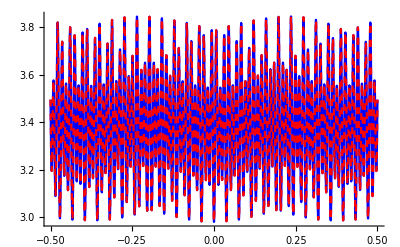
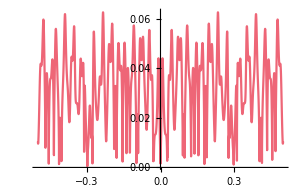
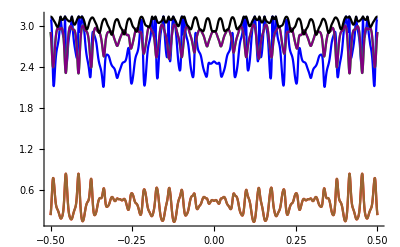
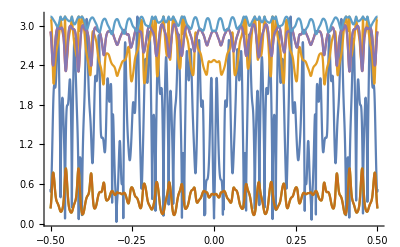

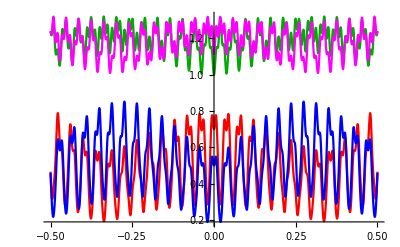
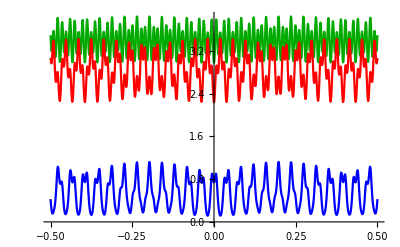
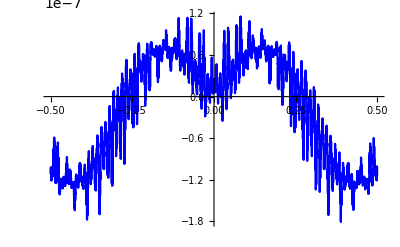
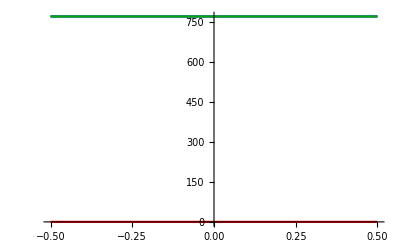

```mathematica
{xmin,xmax}={-0.5,0.5};
{α0,β0,ξ0}={0.7,0.5,1};
{θ0,φ0}={ 0, 0};
name="1";
tiempo = -0.05;

{tmin,tmax}={-10000,10000};
grid = 5;

For[n=3, n≤ 6,n++,
For[ss=1,ss≤ 5, ss++,

graficos = ConstantArray[Green,{grid,grid}];
graficos2 = ConstantArray[Green,{grid,grid}];
graficos3 = ConstantArray[Green,{grid,grid}];

For[ii=1,ii≤grid, ii++,
For[jj=1,jj≤ grid, jj++,

	λnot=RandomReal[{-5,5},{n,n}];
	γnot= RandomComplex[{-2-2 ⅈ,2+2 ⅈ},{n,n}];

	λ = UpperTriangularize[λnot]+Transpose[UpperTriangularize[λnot,1]];
	γ = UpperTriangularize[γnot]+Transpose[UpperTriangularize[γnot,1]];

params=<|"xmin"-> xmin, "xmax"-> xmax,
	       "γ"-> γ,"H0"-> 0,"λ"->λ,
	       "α0"-> α0,"β0"-> β0, "ξ0"-> ξ0, "δ0"-> None,
	       "θ"-> θ0, "φ"-> φ0,
		"3drange"->4,
	       "method"-> "Automatic",
		"name"-> name,"tiempo"-> tiempo|>;

	Quiet[Check[plot[params],graficos[[ii,jj]]=Red]];
	If[λterm2^2 - ( γterm2+γcterm2)^2 ≤ 0,
	graficos2[[ii,jj]] = Red,
	None];
	If[λterm2^2 - ( γterm2+γcterm2)^2 ≤ 0,
	graficos2[[ii,jj]] = Red,
	None];
]];

Export["/Users/enekoaranguren/Documents/lqg/coupling_parameter_spectrum/"<>ToString@n<>"/"<>ToString@ss<>".png",ArrayPlot[graficos]];
Export["/Users/enekoaranguren/Documents/lqg/coupling_parameter_spectrum/"<>ToString@n<>"/"<>ToString@ss<>"_2.png",ArrayPlot[graficos2]];

]];
```